```mathematica
(*ML Data*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLF1.xlsx"];
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

21

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

21

```mathematica
(*fitting to 90% of the data*)
n90=Floor[nΔYVec (0.9)]
```

18

```mathematica
(*Covariates*)

(*Accuracy Energy*)
X1Vec=Data[[1,All,3]];
(*X3Vec=X3Vec^2;*)

(*Accuracy COOL*)
X2Vec=Data[[1,All,4]];

(*Energy Unknowns*)
X3Vec=Data[[1,All,5]];

(*COOL Unknowns*)
X4Vec=Data[[1,All,6]];
```

```mathematica
(*Plot Y - Observed data*)
```

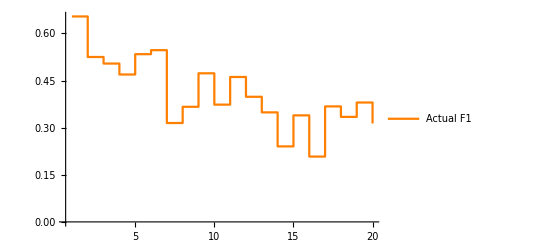

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Orange,PlotLegends->{"Actual F1"}]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=3)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β12 X2[[i]] X3[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]))/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];



Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];



Dβ12=Simplify[D[LnL,β12]];





Dβ21=Simplify[D[LnL,β21]];
Dβ22=Simplify[D[LnL,β22]];
Dβ23=Simplify[D[LnL,β23]];
Dβ24=Simplify[D[LnL,β24]];



Dβ28=Simplify[D[LnL,β28]];
Dβ29=Simplify[D[LnL,β29]];
Dβ30=Simplify[D[LnL,β30]];
Dβ31=Simplify[D[LnL,β31]];



Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ7},{0==Dβ8},{0==Dβ12},{0==Dβ21},{0==Dβ22},{0==Dβ23},{0==Dβ24},{0==Dβ28},{0==Dβ29},{0==Dβ30},{0==Dβ31},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β7,0.1},{β8,0.1},{β12,0.1},{β21,0.1},{β22,0.1},{β23,0.1},{β24,0.1},{β28,0.1},{β29,0.1},{β30,0.1},{β31,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦3⟧ is longer than depth of object.

Part::partd: Part specification X2⟦3⟧ is longer than depth of object.

Part::partd: Part specification X3⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→0.12897,β1→0.0741964,β2→0.233672,β3→0.0367838,β7→0.881433,β8→0.144913,β12→-0.106037,β21→-1.1908,β22→0.13091,β23→-0.0362454,β24→-0.0269249,β28→-0.209134,β29→-0.00513048,β30→0.353132,β31→0.00514079,σ→6.68068×10^102}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β12 X2[[i]] X3[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec};
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]],ΔYVec[[2]]};
For[k=3,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{0.,-0.12903,-0.0193552,-0.0358614,0.0703665,0.00521235,-0.224901,0.048773,0.109755,-0.10686,0.0916926,-0.0641479,-0.0512857,-0.113842,0.0990077,-0.125459,0.158756,-0.0324954,0.0699226,-0.0656786,-0.247434+0.344652 +0.920309 ^2}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.653939,0.524909,0.505554,0.469692,0.540059,0.545271,0.32037,0.369143,0.478898,0.372038,0.463731,0.399583,0.348298,0.234455,0.333463,0.208004,0.36676,0.334265,0.404187,0.338509,0.0910745+0.344652 +0.920309 ^2}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.653939},{2,0.524909},{3,0.505554},{4,0.469692},{5,0.540059},{6,0.545271},{7,0.32037},{8,0.369143},{9,0.478898},{10,0.372038},{11,0.463731},{12,0.399583},{13,0.348298},{14,0.234455},{15,0.333463},{16,0.208004},{17,0.36676},{18,0.334265},{19,0.404187},{20,0.338509},{21,0.0910745+0.344652 +0.920309 ^2}}

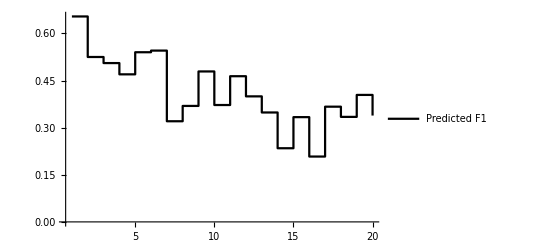

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->0, Joined->True,PlotStyle->Black,PlotRange->All,PlotLegends->{"Predicted F1"}]
```

Show::gcomb: Could not combine the graphics objects in ….

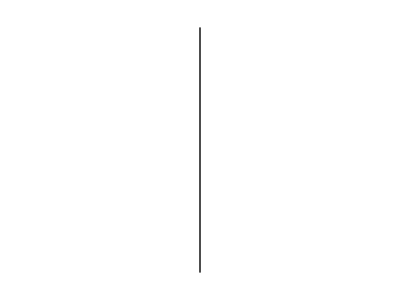
Show[{-Graphics-,-Graphics-},-Graphics-,PlotRange→All]

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)


A=Show[{YObserved,YPredictedPlotInt},Graphics[{Black, Line[{{n90,0},{n90,1}}]}],PlotRange->All]
```

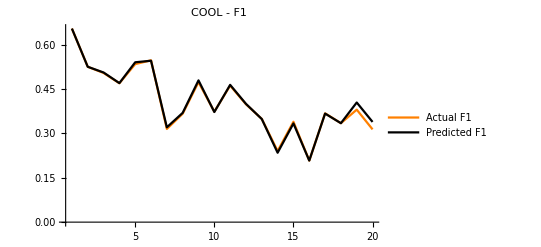

```mathematica
A=ListPlot[{dataPlot,NewPlot},InterpolationOrder->1, Joined->True,PlotStyle->{Orange,Black},PlotRange->All,PlotLegends->{"Actual F1","Predicted F1"},PlotLabel->"COOL - F1"]
```

```mathematica
B=Graphics[{Black, Dashed,Line[{{n90,0},{n90,1}}]}];
```

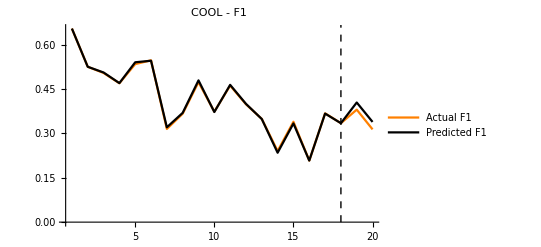

```mathematica
Show[A,B]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.00140928+(-0.0910745+0.655348 -0.920309 ^2)^2

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.00121556+(-0.0910745+0.655348 -0.920309 ^2)^2

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

1/4 (0.00121556+(-0.0910745+0.655348 -0.920309 ^2)^2)

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->6
```

1-10/7 (1-(-0.00140928+(-0.231892+1/21 (0.340542-))^2+(-0.1312+1/21 (0.340542-))^2+(-0.12903+1/21 (0.340542-))^2+(-0.108283+1/21 (0.340542-))^2+(-0.0997716+1/21 (0.340542-))^2+(-0.0666041+1/21 (0.340542-))^2+(-0.0630462+1/21 (0.340542-))^2+(-0.0496092+1/21 (0.340542-))^2+(-0.034831+1/21 (0.340542-))^2+(-0.0333539+1/21 (0.340542-))^2+(-0.0209054+1/21 (0.340542-))^2+(0.+1/21 (0.340542-))^2+(0.0127587+1/21 (0.340542-))^2+(0.0457366+1/21 (0.340542-))^2+(0.051561+1/21 (0.340542-))^2+(0.0647187+1/21 (0.340542-))^2+(0.0880556+1/21 (0.340542-))^2+(0.0987849+1/21 (0.340542-))^2+(0.106673+1/21 (0.340542-))^2+(0.159696+1/21 (0.340542-))^2+(1/21 (0.340542-)+)^2-(-0.0910745+0.655348 -0.920309 ^2)^2)/((-0.231892+1/21 (0.340542-))^2+(-0.1312+1/21 (0.340542-))^2+(-0.12903+1/21 (0.340542-))^2+(-0.108283+1/21 (0.340542-))^2+(-0.0997716+1/21 (0.340542-))^2+(-0.0666041+1/21 (0.340542-))^2+(-0.0630462+1/21 (0.340542-))^2+(-0.0496092+1/21 (0.340542-))^2+(-0.034831+1/21 (0.340542-))^2+(-0.0333539+1/21 (0.340542-))^2+(-0.0209054+1/21 (0.340542-))^2+(0.+1/21 (0.340542-))^2+(0.0127587+1/21 (0.340542-))^2+(0.0457366+1/21 (0.340542-))^2+(0.051561+1/21 (0.340542-))^2+(0.0647187+1/21 (0.340542-))^2+(0.0880556+1/21 (0.340542-))^2+(0.0987849+1/21 (0.340542-))^2+(0.106673+1/21 (0.340542-))^2+(0.159696+1/21 (0.340542-))^2+(1/21 (0.340542-)+)^2))